```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
lT=50;
startT=1;
alist=Table[Flatten[Import["bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
V1=Flatten[Transpose[Table[Flatten[Import["./dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
ρmin=0.;
ρmax=30000.;
```

```mathematica
driv1=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
```

```mathematica
T=Table[Exp[Log[10^-5]-(Log[10^-5]-Log[100])/50*(i-1)]//N,{i,1,lT}];
slop=Table[{SetPrecision[Log[T[[i]]/125.955588],90],SetPrecision[Re[FindFit[Transpose[{-Log[T/125.955588],Log[1/√V1]}][[i;;i+1]],a x+b,{a,b},x][[1]][[2]]],90]},{i,1,lT-1}];
```

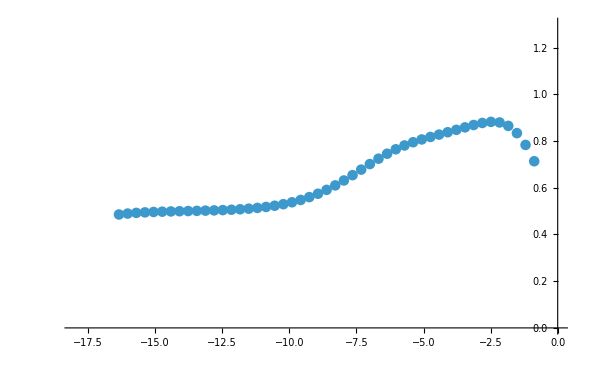

```mathematica
ListPlot[slop,ScalingFunctions->{Automatic,Automatic},PlotRange->{{-18,0},{0.,1.3}}]
```

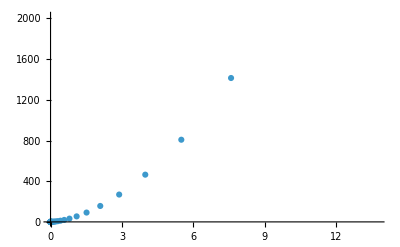

```mathematica
ListPlot[Transpose[{T,V1}],ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
V1
```

{0.000082275667583201517943914762514342237,0.00011252398940015973935295967476350956,0.00015428695758192197605563113181285055,0.00021195217143931897264468544550130551,0.00029158278428838679301781542812280987,0.0004015604989560299926749690427476373,0.00055347741227951233268674879115643975,0.00076337650816052319440501460044455165,0.0010534779465715382725698998214801604,0.0014545912136160373456622281837776892,0.0020094942345363995187683339591921853,0.0027776899934128795443691695654612919,0.0038421373058639274923592254792976293,0.0053188399028733970891079736722103589,0.0073706192307275391406159344646877688,0.01022708909235060995382661537081531,0.014213954102832714875495153845147779,0.019796538324875641159836972727688511,0.027645379253914233283768426110161185,0.038736583254683977218838848694869228,0.054507803681896344710707677769901349,0.077104530113514162284302680276701587,0.10977500486183957466665854555034362,0.15751269483971358692625937582524527,0.2281154407505147883011752864752548,0.33395215886330509115955271740782506,0.49493947398040888148378868484804361,0.74359760466224399679064060327316382,1.1336886723588088984266562585031715,1.7550281069482491142365616474399589,2.7589131435409402234964215259642057,4.4017643215194740069758502732173421,7.1199792080428308703501367185177379,11.658446300489377175274691980030544,19.292115123755415642910200808082657,32.21099191509896539838455278358871,54.195802477621798009088093295865687,91.815514035370180630946091726043989,156.56739075747441233033319914671019,268.72696390981821311506716605247446,464.30984594251728552880983546646099,807.68134129948376916914749713198017,1414.2326160103320030976236229987003,2490.1542380902903826466676971964139,4398.3384248288801032278164300532668,7755.7990420763218406687229501590743,13547.699114873504246074196408618432,23194.470093964756448542798963885774,38440.896517566588481053725750887003,60901.118740560802791427305839543113}